On the new and old physics in the interaction of a radiating electron with the extreme electromagnetic field

M. Jirka, et al, Phys. Rev. A 103, 053114
Notebook: Óscar Amaro, April/May 2022 @ GoLP-EPP

Figure 1
Field components in tight-focusing.

```mathematica
Clear[λ,x,y,z,Bx,Eθ]
Clear[xR,W,W0,r,ϕ,ϕG,R,ρ,k,ω0,ϕ0,ϵ]
Clear[S2,S3,S4,S5,S6]
Clear[C2,C3,C4,C5,C6,C7,C8]
Clear[Eθmax,Bxmax]

λ=0.8; (*[μm] wavelength*)
W0 = 0.424λ; (*[μm] spotsize, not explicit in the paper*)
E0=1; (*[E] maximum field *)
k=2π/λ;(*[μm-1] wavenumber*)
ϵ=λ/(π W0);(*[] focusing parameter*)
xR=k W0^2/2;(*[μm] Rayleigh range*)
r[y_,z_]:=Sqrt[y^2+z^2]; (*[μm] radius*)
ρ[y_,z_]:=r[y,z]/W0; (*[] normalized radius*)
W[x_]:=W0 Sqrt[1+(x/xR)^2];(*[μm] spatially-dependent spotsize*)
R[x_]:=x+xR^2/x;(*[μm] radius of curvature*)
ϕG[x_]=ArcTan[x/xR];
t=0;(*[ω-1] time *)
ϕ0 = 0; (*[] initial phase*)
(*x = 0; (*[μm] focal plane*)*)
ϕ[x_,y_,z_]:=ϕ0+ω0 t-k x-k r[y,z]^2/(2(x+xR^2/x)); (*[] phase *)

(* auxiliary tight focusing expansion terms*)
C2[x_,y_,z_]:=(W0/W[x])^2 Cos[ϕ[x,y,z]+2 ϕG[x]];
C3[x_,y_,z_]:=(W0/W[x])^3 Cos[ϕ[x,y,z]+3 ϕG[x]];
C4[x_,y_,z_]:=(W0/W[x])^4 Cos[ϕ[x,y,z]+4 ϕG[x]];
C5[x_,y_,z_]:=(W0/W[x])^5 Cos[ϕ[x,y,z]+5 ϕG[x]];
C6[x_,y_,z_]:=(W0/W[x])^6 Cos[ϕ[x,y,z]+6 ϕG[x]];
C7[x_,y_,z_]:=(W0/W[x])^7 Cos[ϕ[x,y,z]+7 ϕG[x]];
C8[x_,y_,z_]:=(W0/W[x])^8 Cos[ϕ[x,y,z]+8 ϕG[x]];
(**)
S2[x_,y_,z_]:=(W0/W[x])^2 Sin[ϕ[x,y,z]+2 ϕG[x]];
S3[x_,y_,z_]:=(W0/W[x])^3 Sin[ϕ[x,y,z]+3 ϕG[x]];
S4[x_,y_,z_]:=(W0/W[x])^4 Sin[ϕ[x,y,z]+4 ϕG[x]];
S5[x_,y_,z_]:=(W0/W[x])^5 Sin[ϕ[x,y,z]+5 ϕG[x]];
S6[x_,y_,z_]:=(W0/W[x])^6 Sin[ϕ[x,y,z]+6 ϕG[x]];

(* fields *)
Bx[x_,y_,z_]:= E0 Exp[-r[y,z]^2/W[x]^2]( ϵ^2 (S2[x,y,z]-ρ[y,z]^2 S3[x,y,z])+ϵ^4(S3[x,y,z]/2+ρ[y,z]^2 S4[x,y,z]/2-5ρ[y,z]^4 S5[x,y,z]/4 + ρ[y,z]^6 S6[x,y,z]/4) ) //Quiet(*Bx equation 2*)

Eθ[x_,y_,z_]:=E0 Exp[-r[y,z]^2/W[x]^2](ϵ ρ[y,z] C2[x,y,z] + ϵ^3(ρ[y,z] C3[x,y,z]/2+ρ[y,z]^3C4[x,y,z]/2 ρ[y,z]^5C5[x,y,z]/4) + ϵ^5(3ρ[y,z] C4[x,y,z]/8+3ρ[y,z]^3C5[x,y,z]/8+3ρ[y,z]^5 C6[x,y,z]/16-ρ[y,z]^7 C7[x,y,z]/4+ρ[y,z]^9 C8[x,y,z]/32)) //Quiet(*Eθ equation 3*)

(* find maximum fields for plotting *)
Eθmax=FindMaximum[Abs[Eθ[0,0,z]],{z,0,3λ}][[1]];
Bxmax=FindMaximum[Abs[Bx[x,0,0]],{x,0,3 0.5λ}][[1]];
```

```mathematica
Clear[pltBx,pltEθ,pnts]
pnts=25;
pltBx=ContourPlot3D[Abs[Bx[x λ,y λ,z λ]],{x,-0.5,0.5 },{y,0,1},{z,-1,1},Contours->Table[i,{i,0.5,1,0.1/2}]Bxmax,Mesh->None, MaxRecursion->0,PlotPoints->pnts,AxesLabel->{"x/λ","y/λ","z/λ"},ColorFunction->"BlueGreenYellow",PlotRange->All];
pltEθ=ContourPlot3D[Abs[Eθ[x λ,y λ,z λ]],{x,-0.5,0.5 },{y,0,1},{z,-1,1},Contours->Table[i,{i,0.5,1,0.1/2}]Eθmax,Mesh->None, MaxRecursion->0,PlotPoints->pnts,ColorFunction->"ThermometerColors",PlotRange->All];
Show[{pltBx,pltEθ}]
```

-Graphics3D-

Figure 2
Ratio of electrons reaching α χe^2/3 ~ 1
For fixed χe and varying electron energy, the laser intensity varies accordingly. If the implementation of the equations is correct, then actually we are fixing α χe^2/3 ~ 2.4 (and not 1)...

```mathematica
Clear[χe,ℰe,γe,Wγ,pc,tc,ω0,E0,ℰc,me,c,e,α,ℏ,T,ES,λμm,τ,W0,aS]

W0 = 0.424λμm; (*[μm] spotsize, not explicit in the paper*)

χe=2γe E0/ES;
γe=ℰe/(me c^2);
Wγ=3^(2/3) 28 Gamma[2/3] α me^2 c^4χe^(2/3)  /(54 ℏ ℰe) ;
pc = Wγ tc;
tc=τ/(2Sqrt[2Log[2]]);
ω0=2π c/(λμm 10^-6);
E0=0.855 λμm  Sqrt[I0 10^-18] me ω0 c/e;
ℰc=(1-16/63)^pc  ℰe ;
T=0.67(λμm 10^-6)/c;(*[s] the 0.67 factor is needed to reproduce the results *)

(* physical constants *)
me=9.11 10^-31;(*[Kg]*)
c= 299792458; (*[m/s]*)
e=1.602176634 10^-19; (*[C]*)
α=1/137; (*[]*)
ℏ=1.054571817 10^-34;(*[J s]*)
ES=me^2 c^3/(e ℏ);(*[V/m]*)
aS = 329719; (*[] for λ=0.8*)
```

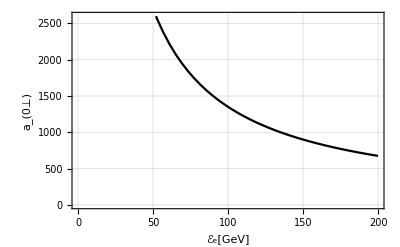

General::munfl: 1/63^5072.25 is too small to represent as a normalized machine number; precision may be lost.

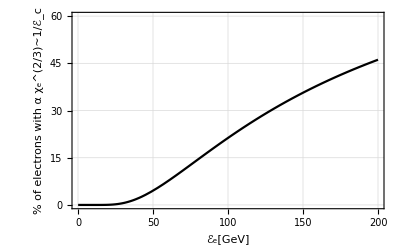

```mathematica
(* required a0⊥ for α χ^2/3=1 *)
Plot[{aS/(2ℰee 10^9 e/( me c^2))(1/α)^1.5},{ℰee,0,200},PlotRange->{{0,200},{0,2600}},Frame->True,ImageSize->400,FrameLabel->{"ℰ_e[GeV]","a_(0⊥)"},PlotStyle->Black,GridLines->Automatic]

Plot[(100 (47/63)^((0.030199136711634034 c^4 me^2 ((√I0 ℰe)/(e ES))^(2/3) α τ)/(ℰe ℏ)) )//.{ℰe->ℰee  10^9 e ,τ->T/2,λμm->0.8, I0->(aS/(2ℰee 10^9 e/( me c^2))(2.4/α)^1.5  /(0.855 λμm))^2 10^18},{ℰee,0.1,200},PlotRange->{{0,200},{0.,60}},Frame->True,ImageSize->400,FrameLabel->{"ℰ_e[GeV]","% of electrons with α χ_e^(2/3)~1/ℰ_c"},PlotStyle->Black,GridLines->Automatic]
```

```mathematica
(* page 3/6 text says α0=960, ℰ=140 GeV -> %=1/3 *)
aS/(2ℰe /( me c^2))(1/α)^1.5 /.{ℰe->140  10^9 e}

(* indeed if the χe is corrected for, this is the percentage obtained *)
(100 (47/63)^((0.030199136711634034 c^4 me^2 ((√I0 ℰe)/(e ES))^(2/3) α τ)/(ℰe ℏ)) )//.{ℰe->140  10^9 e ,τ->T/2,λμm->0.8, I0->(aS/(2ℰe /( me c^2))(2.4/α)^1.5  /(0.855 λμm))^2 10^18}
```

964.975

33.1261